```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica/Ganesh

```mathematica
hbar=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
```

ℏ^2/(2  μ) = 20.7369

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=(-1)^l z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
LECsNUCL=Import["../LECs_nucl_Joki.dat","Table"][[2;;]];

activeLEC=LECsNUCL[[All,{1,2,3}]]
```

{{0.5,-16.3721,4.436},{0.75,-28.6714,12.936},{1,-44.4515,27.245},{1.5,-86.4495,79.22},{2,-142.363,173.925},{3,-295.93,558.493},{4,-505.15,1395.63},{6,-1090.55,6293.03},{8,-1898.55,23937.6},{10,-2929.17,85318.8}}

```mathematica
NormTF[core_?ArrayQ]:=Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]]core[[k]][[1]]core[[l]][[1]] (Pi^2/(4 (core[[i]][[2]]+core[[j]][[2]])(core[[k]][[2]]+core[[l]][[2]])))^(3/2),{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_,Gg_,Hh_]:=Block[{eta2,eta3,w2,w3},
eta2= (8/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(4((1/4)lam^2 Bb + Aa((1/4)lam^2 + 2Gg +2  Bb) + (1/4)lam^2Hh +2 Bb Hh+Gg((1/4)lam^2 +2Hh))^(3/2));
w2= 2(1/4)lam^2(Aa+Hh)(Gg+Bb)/((1/4)lam^2 Bb + Aa((1/4)lam^2+2 Gg+2Bb)+(1/4)lam^2 Hh +2 Bb Hh+Gg((1/4)lam^2+2Hh));
eta3 =(8/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(4((1/4)lam^2 Bb + Gg((1/4)lam^2 + 2Bb)+(1/4)lam^2Hh +2Bb Hh + Aa((1/4)lam^2+2Gg+2Hh))^(3/2));
w3 = 2(1/4)lam^2(Aa+Bb)(Gg+Hh)/((1/4)lam^2 Bb + Gg((1/4)lam^2+2Bb)+(1/4)lam^2 Hh +2Bb Hh+Aa((1/4)lam^2+2Gg+2Hh));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]
];


WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Gg_,Hh_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5/(2(Aa+Bb+Gg+ Hh))^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(2(2(1/4)lam^2+Aa +Bb+ Gg+Hh))^(3/2);
zeta3=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(2(2(1/4)lam^2+Aa +Bb+ Gg+Hh))^(3/2);

a2=(4Hh(2(1/4)lam^2+Bb)+Gg(2(1/4)lam^2 +Bb+Hh)+Aa(2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
b2=(Gg(lam^2+2Bb-2 Hh)+Aa(-4(1/4)lam^2-2Bb+2Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
c2=( Gg(2(1/4)lam^2+Bb+Hh)+Aa(2(1/4)lam^2+4Gg+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));

a3= (4Bb(2(1/4)lam^2+Hh)+Gg(Bb+2(1/4)lam^2+Hh)+Aa(2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4(1/4)lam^2-2Hh)+Aa(4(1/4)lam^2+2Hh-2Bb))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2(1/4)lam^2+Hh)+Aa(4Gg+2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));

-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)-TwoMyOverHBsq Ee)  SphericalBesselJ[0,I b1 r rp]
-4 a1 b1 r rp I Sqrt[3]^-1 SphericalBesselJ[1,I b1 r rp])
+zeta2 SphericalBesselJ[0,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+zeta3 SphericalBesselJ[0,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

Wmat=ConstantArray[0,{Npoints,Npoints}];
wmat=ConstantArray[0,{Npoints,Npoints}];
t1=AbsoluteTime[];
Do[

Aa=a00[[ii]][[2]];Bb=a00[[jj]][[2]];Gg=a00[[kk]][[2]];Hh=a00[[ll]][[2]];
zeta1=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5/(2(Aa+Bb+Gg+ Hh))^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 c0/(2(2(1/4)lam^2+Aa +Bb+ Gg+Hh))^(3/2);
zeta3=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 c0/(2(2(1/4)lam^2+Aa +Bb+ Gg+Hh))^(3/2);

a2=(4Hh(2(1/4)lam^2+Bb)+Gg(2(1/4)lam^2 +Bb+Hh)+Aa(2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
b2=(Gg(lam^2+2Bb-2 Hh)+Aa(-4(1/4)lam^2-2Bb+2Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
c2=( Gg(2(1/4)lam^2+Bb+Hh)+Aa(2(1/4)lam^2+4Gg+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));

a3= (4Bb(2(1/4)lam^2+Hh)+Gg(Bb+2(1/4)lam^2+Hh)+Aa(2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4(1/4)lam^2-2Hh)+Aa(4(1/4)lam^2+2Hh-2Bb))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2(1/4)lam^2+Hh)+Aa(4Gg+2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]];

wmat=ParallelTable[-hDif^3 TwoMyOverHBsq 
-(4 Pi i hDif j hDif) (
zeta1 Exp[-a1 (i hDif)^2-c1 (j hDif)^2] ((-(4 a1^2 (i hDif)^2+b1^2 (j hDif)^2-2 a1)-TwoMyOverHBsq energyMeV)  SphericalBesselJ[0,I b1 (i hDif) (j hDif)]
-4 a1 b1 (i hDif) (j hDif) I Sqrt[3]^-1 SphericalBesselJ[1,I b1 (i hDif) (j hDif)])
+zeta2 SphericalBesselJ[0,I b2 (i hDif) (j hDif)] Exp[-a2 (i hDif)^2-c2 (j hDif)^2]
+zeta3 SphericalBesselJ[0,I b3 (i hDif) (j hDif)] Exp[-a3 (i hDif)^2-c3 (j hDif)^2]
)
,{i,1,Npoints},{j,1,Npoints}]; 

Wmat=Wmat+cij (amat+wmat);

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];
t2=AbsoluteTime[];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

t3=AbsoluteTime[];
usol=LinearSolve[Amat,bcol];
t4=AbsoluteTime[];

Print["t_2-t_1 = ",t2-t1,"   t_4-t_3 = ",t4-t3];

tanDelta= (RiccatiBesselJ[momentum  Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
];
```

```mathematica
SolveSecularParallel[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

(*Wmat=ConstantArray[0,{Npoints,Npoints}];*)

Wmats={};
SetSharedVariable[Wmats];

ParallelDo[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]];

wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 

AppendTo[Wmats,cij (amat+wmat)];

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmats];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum  Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
];
```

```mathematica
GetERE[l_,rMax_,nPoints_,core_,LECc_,energ_:0.001]:=Module[{locall=l},
LECd=0.0;
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecularParallel[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
-Re[TanDelSwave]/Sqrt[mh2 energ ]
]
```

{{-0.122916,0.149553},{-0.341598,1.37211},{-0.515208,7.58087},{-0.776378,22.4113}}

-1.61776

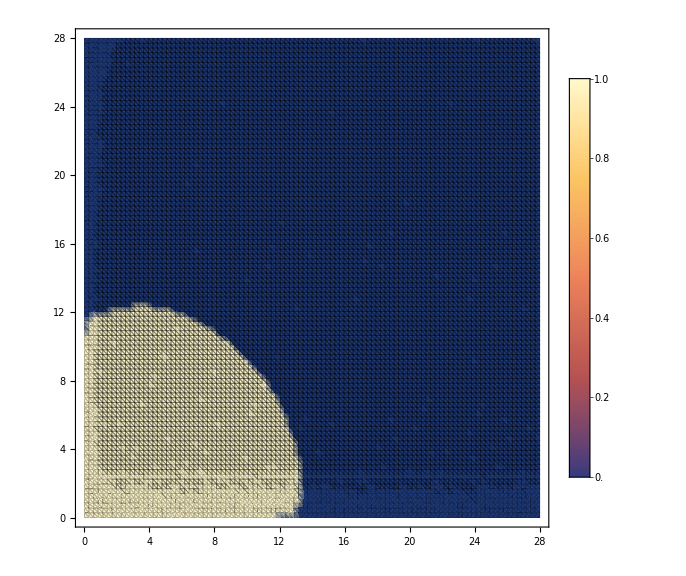
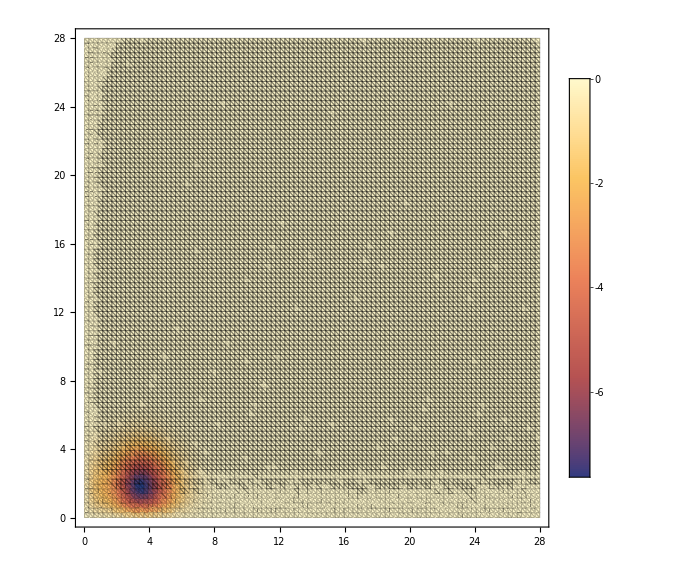
-Graphics- | -Graphics-

```mathematica
lamd=8;
dimerCore=Get["tmp.lst"]
e0Core=Get["E0tmp.lst"]
scaleFactor=1.0;
LECc =scaleFactor Flatten[Select[activeLEC,#[[1]]==lamd&]][[2]];
rMa=28;

energ=0.01;
nR=100;
rMi=0.01;
rR=Range[rMi,rMa,(rMa-rMi)/nR];
nR=Length[rR];
thresh=10^-8;

potnoloc3d={};
potnoloc3d=Flatten[ParallelTable[{rR[[i]],rR[[j]],WnolocTF[rR[[i]],rR[[j]],energ,lamd,LECc,0.0,dimerCore[[1]][[2]],dimerCore[[1]][[2]],dimerCore[[1]][[2]],dimerCore[[1]][[2]],0,mh2]}
,{i,Length[rR]},{j,Length[rR]}],1];

chopedMat=ParallelTable[
If[Abs[Re[potnoloc3d[[i]][[3]]]]>=thresh,{potnoloc3d[[i]][[1]],potnoloc3d[[i]][[2]],1},{potnoloc3d[[i]][[1]],potnoloc3d[[i]][[2]],0}]
,{i,Length[potnoloc3d]}];
Grid[{{
ListDensityPlot[chopedMat,Mesh->All,PlotRange->All,PlotLegends->Automatic,ImageSize->Large]
,
ListDensityPlot[Re[potnoloc3d],Mesh->All,PlotRange->All,PlotLegends->Automatic,ImageSize->Large]
}}]
```

λ = 8   C_0(λ) = -1898.55     R_max = 28     #(grid points) = 35

a_dd = 3.34725 fm

λ = 8   C_0(λ) = -1898.55     R_max = 28     #(grid points) = 40

a_dd = -70.6903 fm

λ = 8   C_0(λ) = -1898.55     R_max = 28     #(grid points) = 45

a_dd = 3.55257 fm

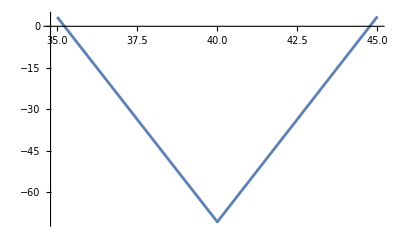

```mathematica
nGrdi=2;
nGrdiMi=35;
nGrdiMa=10+nGrdiMi;
nGr=Range[nGrdiMi,nGrdiMa,Quotient[nGrdiMa-nGrdiMi,nGrdi]];

results={};
(*SetSharedVariable[results,resultsPhases];*)
Do[

Print["λ = ",lamd,"   C_0(λ) = ",LECc,"     R_max = ",rMa,"     #(grid points) = ",nGrd];
tmp=GetERE[lamd,rMa,nGrd,dimerCore,LECc,energ];
AppendTo[results,tmp];
Print["a_dd = ",tmp," fm"];
,{nGrd,nGr}]
ListPlot[Transpose[{nGr,results}],Joined->True]
```

```mathematica
results
aasy=results[[-1]]
Print["a_dd/a =",aasy/(hbar/√(Mm Abs[e0Core]))]
```

{3.34725,-70.6903,3.55257}

3.55257

a_dd/a =0.701637